# Cornell ERL Injector cavities : in.cavity2

```mathematica
root=NotebookDirectory[]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/Phase1B/model/a2/cavity2/

```mathematica
outputCavityFilename = "in.cavity2_grid.bmad";
outputWallFilename = "in.cavity2_wall.bmad";
bmadelename = "in.cavity2";

(*Master switch to flip fields*)
FLIP =True;

If[FLIP,
outputCavityFilename = "in.cavity2_reverse_grid.bmad";
outputWallFilename = "in.cavity2_reverse_wall.bmad";
bmadelename = "in.cavity2_reverse";
]
```

## Options

```mathematica
myplotoptions={BaseStyle->{FontSize->15}, Frame->True};
SetOptions[Plot,myplotoptions];
SetOptions[ListPlot,myplotoptions];
SetOptions[ListLogPlot,myplotoptions];
SetOptions[ListVectorPlot,myplotoptions];
SetOptions[ListDensityPlot,myplotoptions];

cLightN = 299792458.;
μ0N = 4. π 10^-7;
```

## Import

```mathematica
griddatrawfilename="fields_on_grid_1 mm.fls";
surfacedatrawfilename="fields_on_surface.fls";
```

```mathematica
griddatrawheader= Import[root<>griddatrawfilename, "Table"][[1;;6]];
griddatraw= Import[root<>griddatrawfilename, "Table"][[6;;]];
```

```mathematica
griddatrawheader//Grid
```

: | Date:09/19/11.00.00 |  |  |  |  |  |  | 
Mode | number | 2;Frequency | MHz | 1299.99402;Accuracy | 2.38859×10^-8 |  |  | 
R0(CM)= | 0. | Z0(CM)=-1.98000E+01 | NY=102 | NX=484 | DR(CM)= | 0.1 | DZ(CM)= | 0.1
Normalization | W(J)= | 0.001 |  |  |  |  |  | 
R(CM) | Z(CM) | Er(MV/M) | Ez(MV/M) | Hfi(A/M) |  |  |  | 
0. | -19.8 | 0. | -0.00346229 | 0. |  |  |  |

```mathematica
griddat= {1/100*#[[1]], 1/100* #[[2]],10^6* #[[3]], 10^6*#[[4]], μ0N *#[[5]]}&/@griddatraw;
xC=1;
zC=2;
ExC=3;
EzC=4;
ByC=5;

If[FLIP,
flip=Table[1, {5}];
flip⟦zC⟧ = -1;
flip⟦EzC⟧ = -1;
flip⟦ByC⟧ = -1;
griddat=griddat.DiagonalMatrix[flip];
]
```

```mathematica
Min[#[[zC]]&/@griddat]
```

-0.198

```mathematica
Max[#[[zC]]&/@griddat]
```

0.286

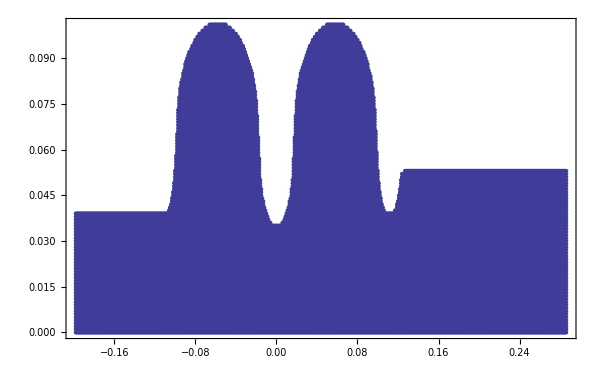

```mathematica
ListPlot[{#[[zC]], #[[xC]]}&/@griddat, ImageSize->600]
```

```mathematica
surfacedatrawheader= Import[root<>surfacedatrawfilename, "Table"][[1;;6]];
surfacedatraw= Import[root<>surfacedatrawfilename, "Table"][[6;;]];
surfacedatrawheader//Grid
```

: | Date:09/19/11 |  |  |  | 
Mode | number | 2;Frequency | MHz | 1299.99402;Accuracy | 2.38859×10^-8
Fields | on | metal |  |  | 
Normalization | W(J)= | 0.001 |  |  | 
ZS(CM) | RS(CM) | ES(MV/M) | HS(A/M) | EZ(MV/M) | ER(MV/M)
-19.8637 | 3.9 | -1.17908×10^-7 | 2.10763 | -9.45205×10^-7 | -6.04439×10^-7

```mathematica
(*Delete duplicate points. *)
surfacedatraw=DeleteDuplicates[surfacedatraw, #1[[1;;2]]==#2[[1;;2]]&];Length[surfacedatraw]
```

517

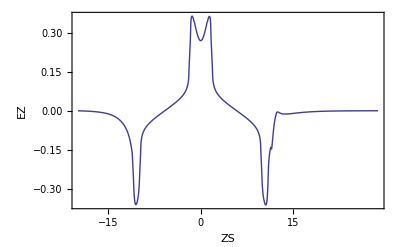

```mathematica
ListPlot[{#⟦1⟧, #⟦3⟧}&/@surfacedatraw, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"ZS", "EZ"}]
```

```mathematica
normalsurfacedat={1/100#⟦2⟧ (*x*),1/100#⟦1⟧(*z*),10^6 #⟦3⟧(*Enormal*), 1/μ0N#⟦4⟧(*Hphi*)}&/@surfacedatraw;
If[FLIP, normalsurfacedat={1/100#⟦2⟧ (*x*),-1/100#⟦1⟧(*z*),10^6 #⟦3⟧(*Enormal*),- 1/μ0N#⟦4⟧(*Hphi*)}&/@surfacedatraw;]
```

```mathematica
contour0={#[[zC]], #[[xC]]}&/@normalsurfacedat;
contourf=Interpolation[
contour0
];
```

```mathematica
Grid[{{"radius entrance (m)", contourf[-0.2]}
,{"radius exit(m)", contourf[0.15]}}, Frame->True]
```

InterpolatingFunction::dmval: Input value {-0.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

radius entrance (m) | 0.039
radius exit(m) | 0.053

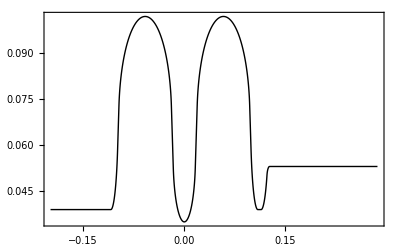

```mathematica
gcontour=ListPlot[contour0, Joined->True, Axes->False, PlotStyle->Black,PlotRange->{All, {0, All}}]
```

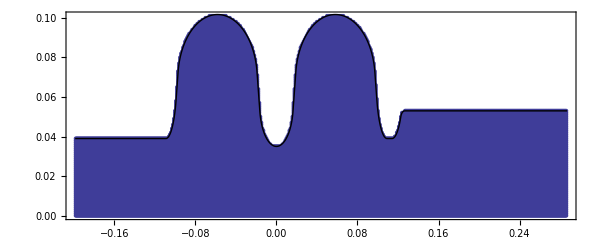

```mathematica
Show[ListPlot[{#[[zC]], #[[xC]]}&/@griddat, ImageSize->600], gcontour, AspectRatio->Automatic]
```

```mathematica
WallData[nsd_ (*normal surface dat*),  vecscale_]:=Module[{contour0,normaldat, Δz,Δr,θ, arrows, gArrows, gWall},
contour0={#⟦1⟧, #⟦2⟧}&/@nsd;
normaldat=Table[
Δz=( nsd[[i+1, zC]]-nsd[[i, zC]]);
Δr=( nsd[[i+1, xC]]-nsd[[i, xC]]);


θ=Arg[Δz+ⅈ Δr]; { nsd[[i,xC]], nsd⟦i,zC⟧,  - nsd⟦i,3⟧Cos[θ], nsd⟦i,3⟧Sin[θ], nsd⟦i,4⟧,-Sin[θ], Cos[θ] } , {i,1,Length[contour0]-1}];

arrows=Arrow[ {{#⟦2⟧, #⟦1⟧}, {#⟦2⟧+vecscale#⟦3⟧ , #⟦1⟧+vecscale#⟦4⟧ }}] &/@normaldat;
gArrows=Graphics[{Arrowheads[Small], arrows}];
gWall=Show[ListPlot[contour0], gArrows, AspectRatio->Automatic];
normaldat[[All,1;;5]]
];
```

```mathematica
walldat=WallData[normalsurfacedat, 0.000000001];
```

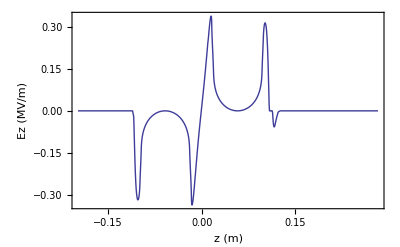

```mathematica
ListPlot[{#⟦zC⟧, 10^-6#⟦EzC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}]
```

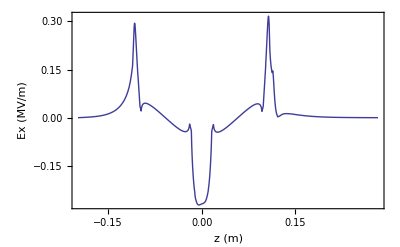

```mathematica
ListPlot[{#⟦zC⟧, 10^-6#⟦ExC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ex (MV/m)"}]
```

## Verify Grid

```mathematica
refdat=griddat;
```

```mathematica
Δz = 0.001;
Δx = 0.001;

nzpad=2;
nxpad=2;
```

```mathematica
xlist=Sort[#[[xC]]&/@refdat, #1<#2&];xlist=Intersection[xlist,xlist];tmpxmax=Max[xlist];xlist=Join[xlist, Table[tmpxmax+n Δx, {n,1,nxpad}]];
zlist=Sort[#[[zC]]&/@refdat, #1<#2&];zlist=Intersection[zlist,zlist];tmpzmax=Max[zlist];zlist=Join[zlist, Table[tmpzmax+n Δz, {n,1,nzpad}]];
xmax = Max[xlist];xmin = Min[xlist];xsize=xmax-xmin;
zmax = Max[zlist];zmin = Min[zlist];zsize=zmax-zmin;
```

```mathematica
Grid[{{,"min (m)","max (m)", "n_pts"},{"x: ",xmin,xmax, Length[xlist]}, {"z: ",zmin,zmax, Length[zlist]}}, Frame->True, Alignment->Left]
```

| min (m) | max (m) | n_pts
x:  | 0. | 0.103 | 104
z:  | -0.198 | 0.288 | 524

```mathematica
izof[z_]:=Round[(z -zmin)/Δz];
ixof[x_]:=Round[(x -xmin)/Δx];
zof[iz_]:=zmin + iz Δz;
xof[ix_]:=xmin + ix Δx;
```

```mathematica
ExGrid={izof[#[[zC]]],ixof[#[[xC]]], #⟦ExC⟧}&/@refdat;
```

```mathematica
izof[zmax]
```

486

```mathematica
ixof[xmax]
```

103

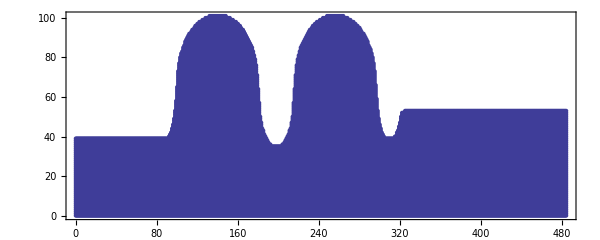

```mathematica
ListPlot[{izof[#[[zC]]],ixof[#[[xC]]]}&/@refdat, ImageSize->600, AspectRatio->Automatic]
```

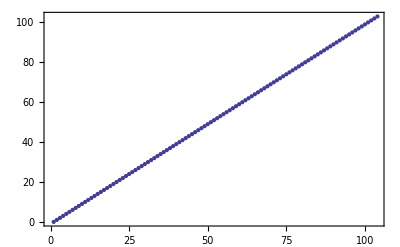

```mathematica
ListPlot[ixof/@xlist]
```

```mathematica
ListPointPlot3D[{{ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[EzC]]}&/@refdat, {ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[ExC]]}&/@refdat}, PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}},AxesLabel->{"x index", "z index", "B (T)"}, BaseStyle->{FontSize->15}]
```

-Graphics3D-

## Extrapolate data beyond edges

```mathematica
(*Make a table of good data points*)
gridGood=Table[{z, x, False}, {z, zmin, zmax, Δz},{x, xmin, xmax, Δx}];
(myix=ixof[#⟦xC⟧];myiz=izof[#⟦zC⟧] ;
gridGood⟦myiz+1, myix+1,3⟧=True)&/@refdat;
```

```mathematica
(*Interpolate data at a point*)
InterpolatedDat[allrefdat_, {z_, x_}]:=Module[{nz, nx, pts, f, ex, ez, by},
(*neighboring intervals to consider*)
nz=4;
nx=4;
pts=Select[allrefdat,Abs[ z-#⟦zC⟧]<nz Δz && Abs[ x-#⟦xC⟧]<nx Δx &];
ex= Interpolation[{#⟦zC⟧, #⟦xC⟧, #⟦ExC⟧}&/@pts, {z, x}];
ez= Interpolation[{#⟦zC⟧, #⟦xC⟧, #⟦EzC⟧}&/@pts, {z, x}];
by= Interpolation[{#⟦zC⟧, #⟦xC⟧, #⟦ByC⟧}&/@pts, {z, x}];
{ex,ez, by}
]
```

```mathematica
GoodNeighbors[datapt_]:=Module[{iz,ix},
ix=ixof[datapt[[xC]]];
iz=izof[datapt[[zC]]];

gridGood[[iz+1;;iz+2, ix+1;;ix+2]]

]
```

```mathematica
edgepts=Flatten[GoodNeighbors/@Select[walldat, zmin+0.01<#[[zC]]<zmax-0.01&], 2];
```

```mathematica
ptstofix={#[[1]], #[[2]]}&/@Select[Intersection[edgepts, edgepts], !#[[3]]&];
```

```mathematica
extrapolateddat= (Flatten[{#⟦2⟧, #⟦1⟧, InterpolatedDat[refdat, {#⟦1⟧, #⟦2⟧}]}])&/@ptstofix;//Quiet
```

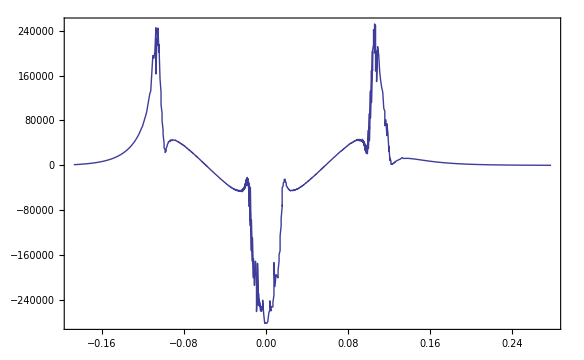

```mathematica
ListPlot[{#[[zC]], #[[ExC]]}&/@extrapolateddat, PlotRange->All, Joined->True]
```

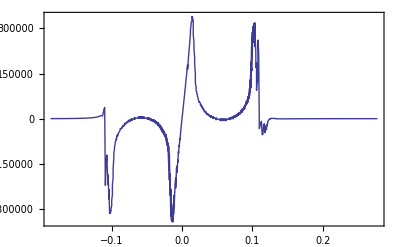

```mathematica
ListPlot[{#[[zC]], #[[EzC]]}&/@extrapolateddat, PlotRange->All, Joined->True]
```

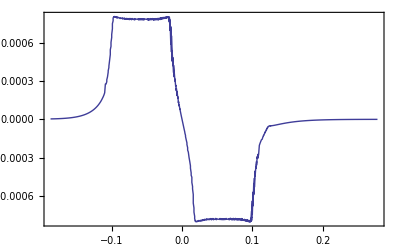

```mathematica
ListPlot[{#[[zC]], #[[ByC]]}&/@extrapolateddat, PlotRange->All, Joined->True]
```

## Make Bmad Grid

```mathematica
fieldmapdir =root;
tmpdir="~/Desktop/";
griddatafilename = outputCavityFilename;
wallfilename = outputWallFilename;
frequency  = 1.3 10^9(* Hz *);

axisdat=Select[refdat, #[[xC]]==0&];
maxEz0=Max[axisdat[[All,EzC]]];

setmaxEz0 =1.0;
fieldscale=setmaxEz0/maxEz0; 

note={"! Maximum on-axis Ez = "<>ToString[fieldscale*maxEz0, FortranForm]<>" V/m"};
```

```mathematica
(*pt format: pt(ir, iz) = ( (ErRe,ErIm), (0,0), (EzRe,EzIm), (0,0), (ErRe,ErIm), (0,0), (BϕRe, BϕIm) , (0,0) ) *)
MakeBmadGrid[dat_]:=Module[{header, body, ptlist},
header = {"{ "};

body = {
{"type = rotationally_symmetric_rz,"},
{"r0 = (",xmin,"," ,0 ,")," },
{"dr = (", Δx,",", Δz, "),"}
};

ptlist ={
"pt(", ixof[ #⟦xC⟧  ], "," ,izof[#⟦zC⟧]  ,") = ( ",
	"(" ,ToString[fieldscale*#⟦ExC⟧, FortranForm],", 0 ), (0,0), ",
			"(", ToString[fieldscale*#⟦EzC⟧, FortranForm],", 0 ), ",
	" (0,0), ( 0, ",ToString[fieldscale* #⟦ByC⟧ , FortranForm], "), (0,0))", ","}&/@dat;
ptlist[[-1,-1]] = "}";
Join[header,note, body,  ptlist]

]
```

```mathematica
(*Use additional extrapolated data*)
griddata=MakeBmadGrid[refdat~Join~extrapolateddat ];
```

```mathematica
Export[tmpdir<>griddatafilename ,griddata, "Table", "FieldSeparators"->""];
Run["mv "<>tmpdir<>griddatafilename<>" "<>root<>griddatafilename];
```

### Wall file

```mathematica
zmax-zmin
```

0.486

```mathematica
nwallpoints = 500;
zmaxpad=0.004;
zrheader= {{"z(m)", "wall_radius(m)"}};
zrlist=Table[{z-zmin, contourf[z]}, {z, zmin, zmax-zmaxpad,((zmax-zmaxpad)-zmin)/(nwallpoints -1)}];Length[zrlist]
```

500

```mathematica
sectionheader={{bmadelename<>"[wall] = {"}};
sectionlist={"section = { s = ", #⟦1⟧, ", v(1) = {0.0, 0.0, " , #⟦2⟧, "} }," }&/@zrlist;
sectionlist[[-1,-1]] = "}}}";
```

```mathematica
(sectionheader~Join~sectionlist)[[1;;10]]
```

{{in.cavity2_reverse[wall] = {},{section = { s = ,0.,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.000965932,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.00193186,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.0028978,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.00386373,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.00482966,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.00579559,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.00676152,, v(1) = {0.0, 0.0, ,0.053,} },},{section = { s = ,0.00772745,, v(1) = {0.0, 0.0, ,0.053,} },}}

```mathematica
Export[fieldmapdir <>wallfilename ,sectionheader~Join~sectionlist, "Table", "FieldSeparators"->""];
```

## EM Field query

```mathematica
fieldquerydir=root
```

/Volumes/accuser/cem52/erl/CERL/lattice_devel/model/in_grid/L0_cavity2/

```mathematica
tmpdir = "~/Desktop/";
```

```mathematica
it = 1;
ix = 2;
iy =3;
is = 4;
iEx=5;
iEy=6;
iEs=7;
iBx=8;
iBy=9;
iBs=10;
```

### Field on axis

```mathematica
selebeg=0.0;

smin =0+selebeg;
smax = 0.48+selebeg
myt=0;
myx=0.0;
myy=0.0;
sampledat=Table[{myt, myx, myy, s}, {s, smin, smax, (smax-smin)/100}];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

0.48

/Volumes/accuser/cem52/erl/CERL/lattice_devel/model/in_grid/L0_cavity2/querypoints.dat

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

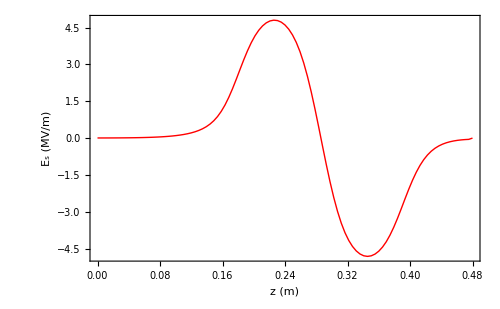

```mathematica
g1=ListPlot[{#[[is]],  10^-6#[[iEs]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
Show[g1, PlotRange->All, FrameLabel->{"z (m)", "E_s (MV/m)"}, ImageSize->500]
```

### Field in time

```mathematica
freq=(1.3 10^9);

tmin=0;
tmax = 1/(1.3 10^9);
mys = 0.23;
myx=0.05;
myy=0.0;
sampledat=Table[{t, myx, myy, mys}, {t, tmin, tmax, (tmax-tmin)/100}];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

$Aborted

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

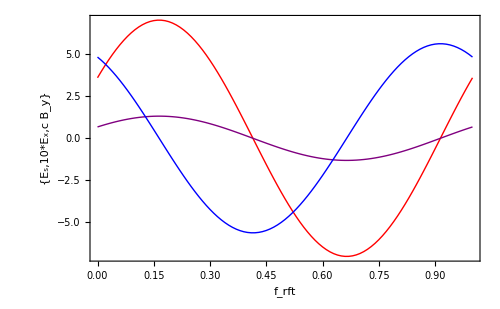

```mathematica
g1=ListPlot[{
{#[[it]]*freq,  10^-6#[[iEs]]}&/@dat,
{#[[it]]*freq,  10 10^-6#[[iEx]]}&/@dat,
{#[[it]]*freq,  10^-6 cLightN#[[iBy]]}&/@dat
}, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->{Red,Purple, Blue}];
Show[g1, PlotRange->All, FrameLabel->{"f_rft",{ Style["E_s",Red], Style["10*E_x",Purple], Style["c B_y", Blue]}}, ImageSize->500]
```

### Field on surface

```mathematica
selebeg=0.0;
myt=0;
myy=0.0;
sampledat=Select[{myt,#⟦xC⟧,myy, #⟦zC⟧-zmin}&/@walldat, 0<#⟦4⟧<0.48&];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"];
```

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

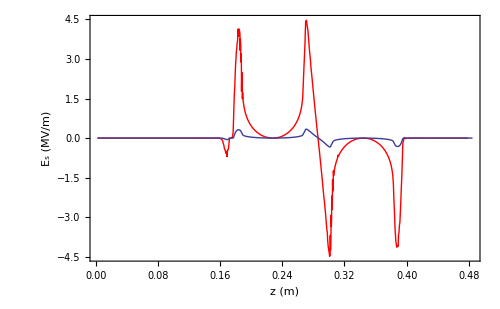

```mathematica
g1=ListPlot[{#[[is]],  10^-6#[[iEs]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#⟦zC⟧-zmin, 10^-6#⟦EzC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}];
Show[g1,g2, PlotRange->All, FrameLabel->{"z (m)", "E_s (MV/m)"}, ImageSize->500]
```

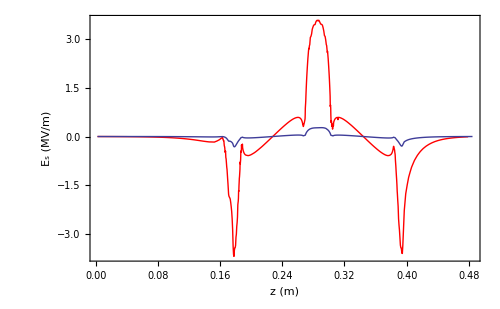

```mathematica
g1=ListPlot[{#[[is]],  10^-6#[[iEx]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#⟦zC⟧-zmin,  10^-6#⟦ExC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}];
Show[g1,g2, PlotRange->All, FrameLabel->{"z (m)", "E_s (MV/m)"}, ImageSize->500]
```

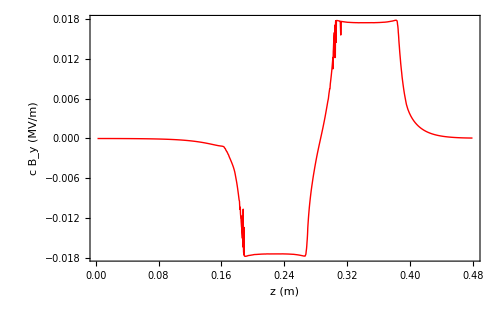

```mathematica
g1=ListPlot[{#[[is]],-#[[iBy]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#⟦zC⟧-zmin, #⟦ByC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}];
Show[g1,PlotRange->All, FrameLabel->{"z (m)", "c B_y (MV/m)"}, ImageSize->500]
```

### Field on a flat grid

```mathematica
selebeg=0;

smin =0+selebeg;
smax = 0.48+selebeg;
myt=0;
myx=0.03;
xmax = 0.1;
nx=50;
ns=200;
xstep=(xmax-xmin)/(nx-1);
 sstep=(smax-smin)/(ns-1);

isof[s_]:=Round[(s-smin)/sstep];
ixof[x_]:=Round[(x -xmin)/xstep];
zof[is_]:=smin + is sstep;
xof[ix_]:=xmin + ix xstep;

sampledat=Flatten[Table[{myt, x, myy, s}, {x,xmin,xmax,xstep},{s, smin, smax,sstep}], 1];Length[sampledat]
```

10000

```mathematica
Export[tmpdir<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"];
Run["mv "<>tmpdir<>"querypoints.dat"<>" "<>root<>"querypoints.dat"];
```

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];Length[dat]
```

10000

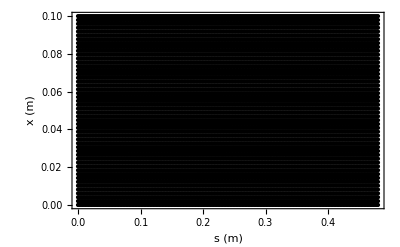

```mathematica
ListPlot[ {#[[is]], #[[ix]]}&/@dat, Frame->True, FrameLabel->{"s (m)", "x (m)"}, BaseStyle->{FontSize->15}, PlotStyle->Black]
```

```mathematica
ListPointPlot3D[{{#⟦is⟧, #⟦ix⟧, #⟦iEs⟧}&/@dat, {#⟦is⟧, #⟦ix⟧, #⟦iEx⟧}&/@dat} , PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}}]
```

-Graphics3D-

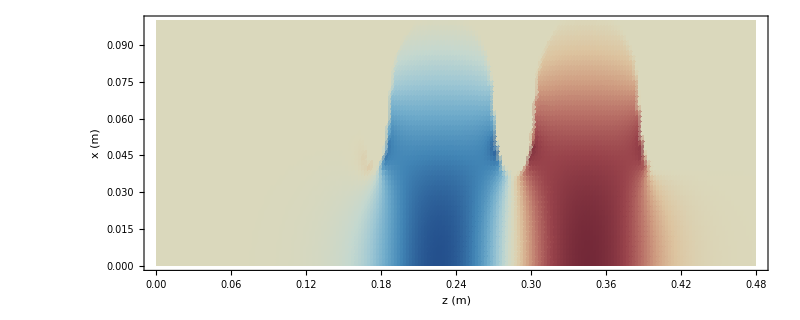

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iEs⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax}}, ColorFunction->"RedBlueTones", FrameLabel->{"z (m)", "x (m)"}],ImageSize->800]
```

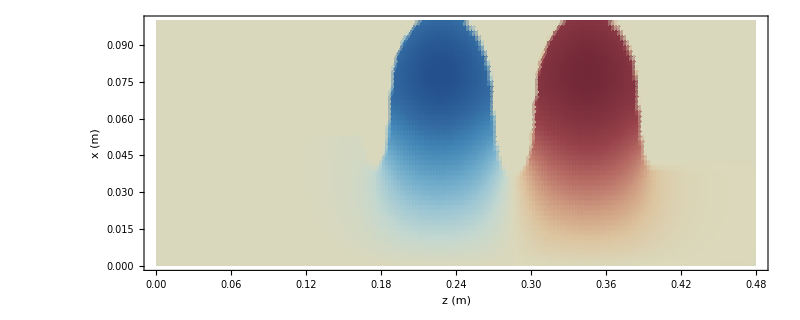

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iBy⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax},All}, ColorFunction->"RedBlueTones",FrameLabel->{"z (m)", "x (m)"}, PlotRange->All],ImageSize->800]
```